```mathematica
Needs["H5`","M5/src/H.m"];
Needs["A5`","M5/src/A.m"];
Needs["A4`","M4/src/A.m"];
Needs["H4`","M4/src/H.m"];
Needs["H3`","M3/src/H.m"];
```

PCA Example 1

```mathematica
(* number of points in both source and target*)
numPoints=100;
(* source: an ellipse with some noise *)
test2DSrc=Table[{2Cos[a],Sin[a]}+{RandomReal[.1],RandomReal[.1]},{a,0,2π,2π/numPoints}];
srcC=getCentroid[test2DSrc];
srcPCA=getPCA[test2DSrc,srcC];
(* targets: rotated and translated sources *)
shift={1,2};angle=0.3;
test2DTgt1=Map[(#+shift)&,Transpose[Rot[angle].Transpose[test2DSrc]]];
tgt1C=getCentroid[test2DTgt1];
tgt1PCA=getPCA[test2DTgt1,tgt1C];
shift={-1,2};angle=2;
test2DTgt2=Map[(#+shift)&,Transpose[Rot[angle].Transpose[test2DSrc]]];
tgt2C=getCentroid[test2DTgt2];
tgt2PCA=getPCA[test2DTgt2,tgt2C];
```

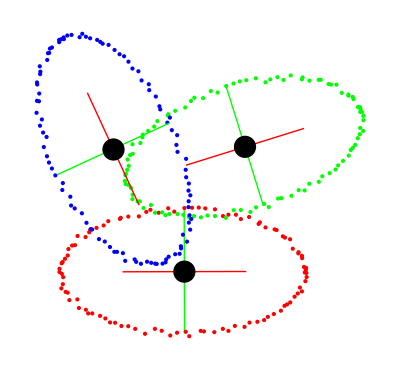

```mathematica
Show[{
	showPoints2D[test2DSrc,RGBColor[1,0,0]],showAxes2D[srcC,srcPCA],
	showPoints2D[test2DTgt1,RGBColor[0,1,0]],showAxes2D[tgt1C,tgt1PCA],
	showPoints2D[test2DTgt2,RGBColor[0,0,1]],showAxes2D[tgt2C,tgt2PCA]}]
```

PCA Example 2

```mathematica
(* number of points in both source and target*)
numPoints=400;
(* source: an ellipsoid with some noise *)
sqrtnum=Sqrt[numPoints/2];
test3DSrc=Flatten[Table[
{2Cos[b]Cos[a],Cos[b]Sin[a],.5Sin[b]}+{RandomReal[.1],RandomReal[.1],RandomReal[.1]},{a,0,2π,π/sqrtnum},{b,-π/2+.2,π/2-.2,(π-.4)/sqrtnum}],1];
src3DC=getCentroid[test3DSrc];
src3DPCA=getPCA[test3DSrc,src3DC];
(* targets: rotated and translated sources *)
shift={1,1.5,1};angleX=0.3;angleY=0.7;
test3DTgt1=Map[(#+shift)&,Transpose[RotY[angleY].RotX[angleX].Transpose[test3DSrc]]];
tgt3D1C=getCentroid[test3DTgt1];
tgt3D1PCA=getPCA[test3DTgt1,tgt3D1C];
shift={-1,2,-1};angleX=0.3;angleY=-2;
test3DTgt2=Map[(#+shift)&,Transpose[RotY[angleY].RotX[angleX].Transpose[test3DSrc]]];
tgt3D2C=getCentroid[test3DTgt2];
tgt3D2PCA=getPCA[test3DTgt2,tgt3D2C];
```

```mathematica
Show[{
	showPoints3D[test3DSrc,RGBColor[1,0,0]],showAxes3D[src3DC,src3DPCA],
	showPoints3D[test3DTgt1,RGBColor[0,1,0]],showAxes3D[tgt3D1C,tgt3D1PCA],
	showPoints3D[test3DTgt2,RGBColor[0,0,1]],showAxes3D[tgt3D2C,tgt3D2PCA]}]
```

-Graphics3D-

PCA align

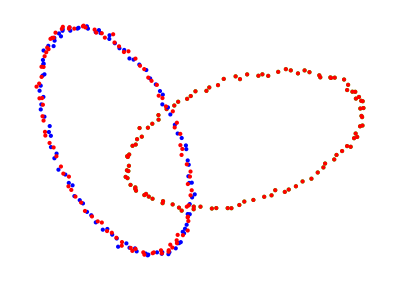

```mathematica
Show[{
	showPoints2D[test2DTgt1,RGBColor[0,1,0]],showPoints2D[alignPCA[test2DSrc,test2DTgt1],RGBColor[1,0,0]],
	showPoints2D[test2DTgt2,RGBColor[0,0,1]],showPoints2D[alignPCA[test2DSrc,test2DTgt2],RGBColor[1,0,0]]
}]
```

```mathematica
Show[{
	showPoints3D[test3DTgt1,RGBColor[0,1,0]],showPoints3D[alignPCA[test3DSrc,test3DTgt1],RGBColor[1,0,0]],
	showPoints3D[test3DTgt2,RGBColor[0,0,1]],showPoints3D[alignPCA[test3DSrc,test3DTgt2],RGBColor[1,0,0]]
}]
```

-Graphics3D-

SVD align

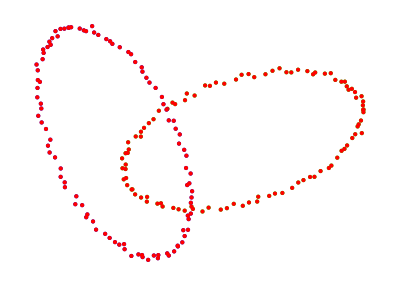

```mathematica
Show[{
	showPoints2D[test2DTgt1,RGBColor[0,1,0]],showPoints2D[alignSVD[test2DSrc,test2DTgt1],RGBColor[1,0,0]],
	showPoints2D[test2DTgt2,RGBColor[0,0,1]],showPoints2D[alignSVD[test2DSrc,test2DTgt2],RGBColor[1,0,0]]
}]
```

```mathematica
Show[{
	showPoints3D[test3DTgt1,RGBColor[0,1,0]],showPoints3D[alignSVD[test3DSrc,test3DTgt1],RGBColor[1,0,0]],
	showPoints3D[test3DTgt2,RGBColor[0,0,1]],showPoints3D[alignSVD[test3DSrc,test3DTgt2],RGBColor[1,0,0]]
}]
```

-Graphics3D-

ICP

```mathematica
pts1=Table[RandomReal[1],{i,50},{2}];
pts2=Table[RandomReal[1],{i,100},{2}];
```

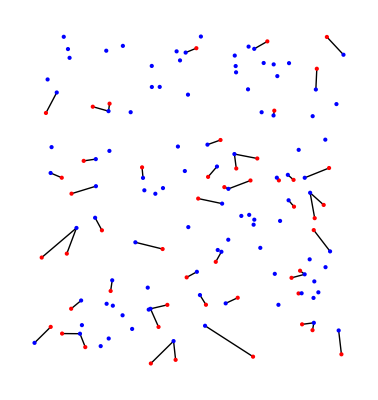

```mathematica
Show[{showCorr2D[pts1,getClosestPoints[pts1,pts2]],showPoints2D[pts1,Red],showPoints2D[pts2,Blue]}]
```

```mathematica
pts1=Table[RandomReal[1],{i,50},{3}];
pts2=Table[RandomReal[1],{i,100},{3}];
```

```mathematica
Show[{showCorr3D[pts1,getClosestPoints[pts1,pts2]],showPoints3D[pts1,Red],showPoints3D[pts2,Blue]}]
```

-Graphics3D-

```mathematica
test2DTgtNoise=Join[test2DTgt1,
Table[{RandomReal[{-2,-.5}],RandomReal[{2,3}]},{i,20}]];
```

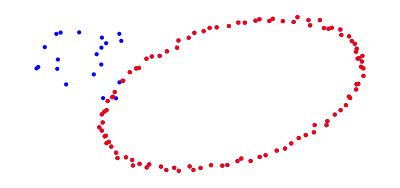

```mathematica
Show[{
	showPoints2D[test2DTgtNoise,RGBColor[0,0,1]],showPoints2D[alignICP[test2DSrc,test2DTgtNoise],RGBColor[1,0,0]]
}]
```

```mathematica
test3DTgtNoise=Join[test3DTgt1,
Table[{RandomReal[{-1.5,1.5}],RandomReal[{2,3}],RandomReal[{2,3}]},{i,50}]];
```

```mathematica
Show[{
	showPoints3D[test3DTgtNoise,RGBColor[0,0,1]],showPoints3D[alignICP[test3DSrc,test3DTgtNoise],RGBColor[1,0,0]]
}]
```

-Graphics3D-

```mathematica
squareCurve={{{0.,1.},{-1.,0.},{0.,-1.},{1.,0.}},{{1,2},{2,3},{3,4},{4,1}}};
squareVinds={1,3};
squareTgts={squareCurve⟦1,1⟧,squareCurve⟦1,3⟧};
```

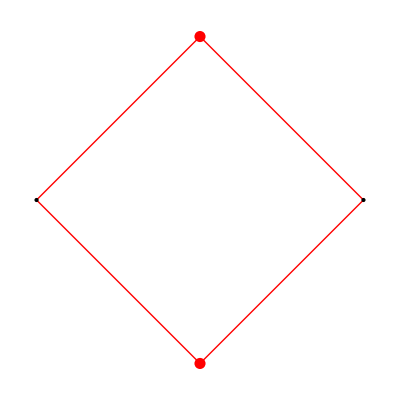

```mathematica
Show[{showCurveWithPoints[squareCurve,Red],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts]}]
```

```mathematica
squareCurve2=deformLaplace[squareCurve,squareVinds,squareTgts,1,True];
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0
-1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 1 | -1/2 | 0 | 0 | 0 | 0
-1/2 | 0 | -1/2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1/2 | 0 | -1/2
0 | 0 | 0 | 0 | -1/2 | 1 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 1 | -1/2
0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 1)

(0.
0.
1.
-1.
0.
-1.
0.
1.
1.
0.
-1.
0.)

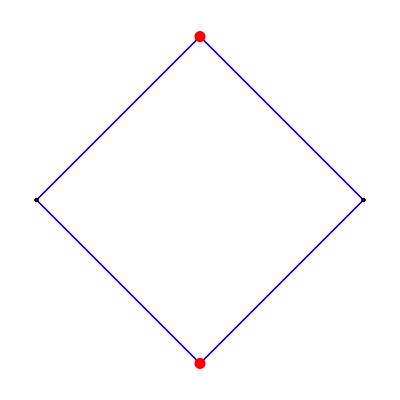

```mathematica
Show[{
	showCurveWithPoints[squareCurve,Red],
	showCurveWithPoints[squareCurve2,Blue],
	showHandles[squareCurve⟦1,squareVinds⟧,squareTgts]}]
```

```mathematica
squareTgts2={squareCurve⟦1,1⟧,squareCurve⟦1,3⟧+{1,0}};
```

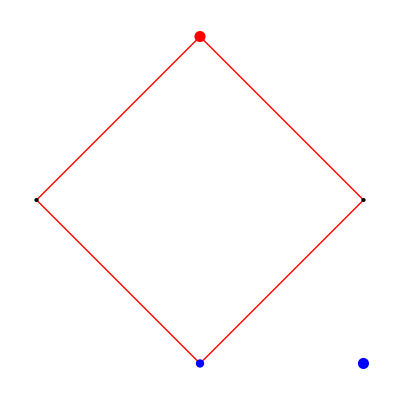

```mathematica
Show[{showCurveWithPoints[squareCurve,Red],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

```mathematica
squareCurve3=deformLaplace[squareCurve,squareVinds,squareTgts2,1];
```

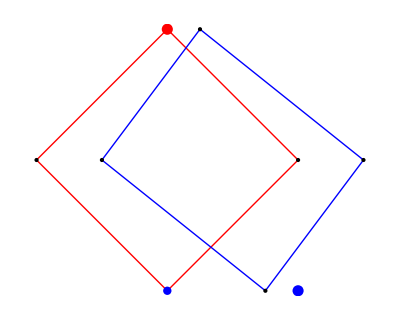

```mathematica
Show[{
	showCurveWithPoints[squareCurve,Red],
	showCurveWithPoints[squareCurve3,Blue],
	showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

```mathematica
squareCurve3=deformLaplace[squareCurve,squareVinds,squareTgts2,.1];
```

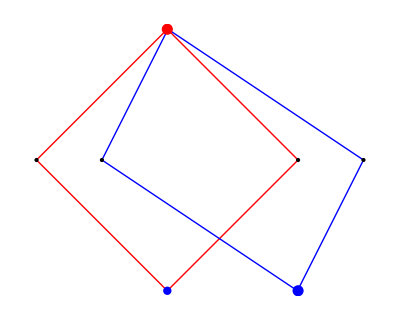

```mathematica
Show[{
	showCurveWithPoints[squareCurve,Red],
	showCurveWithPoints[squareCurve3,Blue],
	showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

```mathematica
mCurve={{{0.,0.},{1.,1.},{2.,0.},{3.,1.},{4.,0.}},{{1,2},{2,3},{3,4},{4,5}}};
mVinds={1,5};
mTgts={mCurve⟦1,1⟧,mCurve⟦1,5⟧};
```

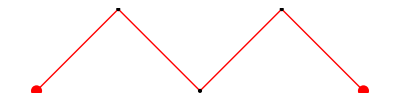

```mathematica
Show[{showCurveWithPoints[mCurve,Red],showHandles[mCurve⟦1,mVinds⟧,mTgts]}]
```

```mathematica
mCurve2=deformLaplace[mCurve,mVinds,mTgts,1];
```

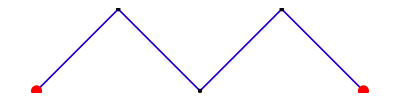

```mathematica
Show[{
	showCurveWithPoints[mCurve,Red],
	showCurveWithPoints[mCurve2,Blue],
	showHandles[mCurve⟦1,mVinds⟧,mTgts]}]
```

```mathematica
numPoints=100;numBumps=15;
starCurve={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]}*(1+.1*Sin[2*numBumps*π/numPoints*i]),{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
starVinds={1,numPoints/4,3*numPoints/4};
starTgts={starCurve⟦1,1⟧+{.3,0.1},starCurve⟦1,starVinds⟦2⟧⟧,starCurve⟦1,starVinds⟦3⟧⟧};
```

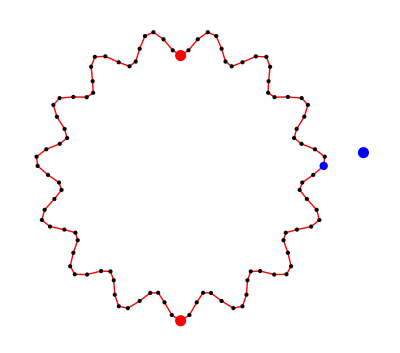

```mathematica
Show[{showCurveWithPoints[starCurve,Red],showHandles[starCurve⟦1,starVinds⟧,starTgts]}]
```

```mathematica
starCurve2=deformLaplace[starCurve,starVinds,starTgts,1];
```

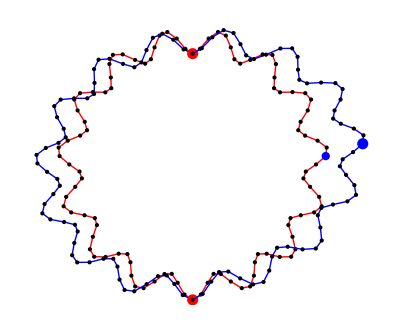

```mathematica
Show[{
	showCurveWithPoints[starCurve,Red],
	showCurveWithPoints[starCurve2,Blue],
	showHandles[starCurve⟦1,starVinds⟧,starTgts]}]
```

```mathematica
Manipulate[
tgts={pt,starCurve⟦1,starVinds⟦2⟧⟧,starCurve⟦1,starVinds⟦3⟧⟧};
Show[{showCurve[starCurve,Red],
showCurve[deformLaplace[starCurve,starVinds,tgts,w],Blue],
showHandles[starCurve⟦1,starVinds⟧,starTgts]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{{pt,starCurve⟦1,1⟧},{-1.5,-1.5},{1.5,1.5},Locator},
{{w,1},1,1000}]
```

```mathematica
numPoints=100;numBumps=5;
springCurve={N[Table[{i/numPoints,5*Sin[2π*i*numBumps/numPoints]/numPoints},{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints-1}]};
springVinds={1,numPoints};
springTgts={First[springCurve⟦1⟧],Last[springCurve⟦1⟧]+{(√2)/2-1,-(√2)/2}};
```

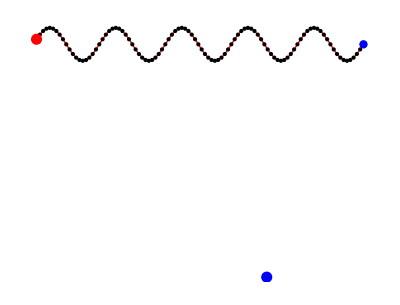

```mathematica
Show[{showCurveWithPoints[springCurve,Red],showHandles[springCurve⟦1,springVinds⟧,springTgts]}]
```

```mathematica
springCurve2=deformLaplace[springCurve,springVinds,springTgts,1];
```

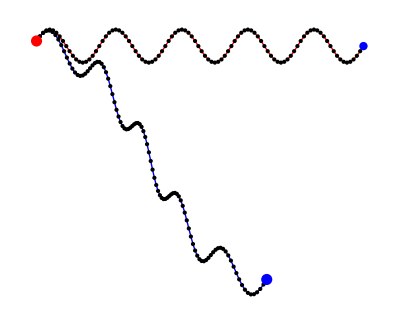

```mathematica
Show[{showCurveWithPoints[springCurve,Red],showCurveWithPoints[springCurve2,Blue],showHandles[springCurve⟦1,springVinds⟧,springTgts]}]
```

```mathematica
Manipulate[
tgts={First[springCurve⟦1⟧],pt};
Show[{showCurve[springCurve,Red],
showCurve[deformLaplace[springCurve,springVinds,tgts,w],Blue],
showHandles[springCurve⟦1,springVinds⟧,tgts]},PlotRange->{{-.2,1.2},{-.5,.5}}],{{pt,Last[springCurve⟦1⟧]},{-.2,-.5},{1.2,.5},Locator},
{{w,1},1,1000}]
```

```mathematica
Manipulate[
tgts={pt,starCurve⟦1,starVinds⟦2⟧⟧,starCurve⟦1,starVinds⟦3⟧⟧};
Show[{showCurve[starCurve,Red],
showCurve[deformLaplaceRot[starCurve,starVinds,tgts,w],Blue],
showHandles[starCurve⟦1,starVinds⟧,starTgts]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{{pt,starCurve⟦1,1⟧},{-1.5,-1.5},{1.5,1.5},Locator},
{{w,1},1,1000}]
```

```mathematica
Manipulate[
tgts={First[springCurve⟦1⟧],pt};
Show[{showCurve[springCurve,Red],
showCurve[deformLaplaceRot[springCurve,springVinds,tgts,w],Blue],
showHandles[springCurve⟦1,springVinds⟧,tgts]},PlotRange->{{-.2,1.2},{-.5,.5}}],{{pt,Last[springCurve⟦1⟧]},{-.2,-.5},{1.2,.5},Locator},
{{w,1},1,1000}]
```

Problem 2

```mathematica
boneSrc=Get["M5/dat/bone_atlas.txt"];
boneTgt={
	Get["M5/dat/bone_test1.txt"],
	Get["M5/dat/bone_test2.txt"],
	Get["M5/dat/bone_test3.txt"]
};
boneRst={
	Map[(alignCC[alignPCA,#,boneSrc])&,boneTgt],
	Map[(alignCC[alignICP,#,boneSrc])&,boneTgt]
};
```

```mathematica
Manipulate[
	Show[{If[so,showSurface[boneSrc,RGBColor[1,0,0]],Nothing],showSurface[If[sr,boneRst[[m,t]],boneTgt[[t]]]]}],
	{{t,1,"Test"},{1->"bone_test1.txt",2->"bone_test2.txt",3->"bone_test3.txt"},ControlType->PopupMenu},
	{{m,1,"Method"},{1->"alignPCA",2->"alignICP"}},
	{{so,True,"Show Origin"},{True,False}},
	{{sr,True,"Display"},{True->"Result",False->"Target"}}]
```

```mathematica
nstarCurve=alignLaplace[starCurve,starCurve2,100,.1];
```

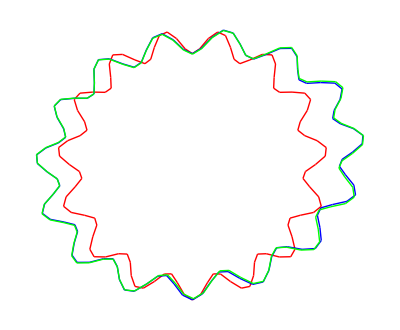

```mathematica
Show[{showCurve[starCurve,Red],showCurve[starCurve2,Blue],showCurve[nstarCurve,Green]}]
```

```mathematica
brainTgt=Get["M5/dat/brain_atlas.txt"];
brainSrc={
	Get["M5/dat/brain_test1.txt"],
	Get["M5/dat/brain_test2.txt"],
	Get["M5/dat/brain_test3.txt"],
	Get["M5/dat/brain_test4.txt"]
};
brainRst=Map[{
	#,
	alignCC[alignPCA,#,brainTgt],
	alignCC[alignICP,#,brainTgt],
	Null
}&,brainSrc];
```

```mathematica
Do[brainRst[[i,4]]=deformLaplaceRot[
	brainRst[[i,3]],
	Range[Length[brainRst[[i,3,1]]]],
	getClosestPoints[brainRst[[i,3,1]],brainTgt[[1]]],
	100],
{i,4}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{117525.,0.,592.282,42.1223},{0.,117525.,42.1223,-592.282},{592.282,42.1223,3.,0.},{42.1223,-592.282,0.,3.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{119993.,0.,598.28,45.127},{0.,119993.,45.127,-598.28},{598.28,45.127,3.,0.},{45.127,-598.28,0.,3.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{94601.9,0.,530.779,45.5743},{0.,94601.9,45.5743,-530.779},{530.779,45.5743,3.,0.},{45.5743,-530.779,0.,3.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
Manipulate[
	Show[{
		If[MemberQ[s,1],showCurve[brainSrc[[t]],RGBColor[0,1,0]],Nothing],
		If[MemberQ[s,2],showCurve[brainTgt,RGBColor[1,0,0]],Nothing],
		If[MemberQ[s,3],showCurve[brainRst[[t,p]],RGBColor[0,0,1]],Nothing]}],
	{{t,1,"test"},{1,2,3,4}},
	{{p,3,"step"},{1->"Init",2->"PCA",3->"ICP",4->"Laplacian"}},
	{{s,{1,2,3},"show"},{1->"source",2->"target",3->"result"},ControlType->TogglerBar}]
```